```mathematica
(1/(80*365))/((1/(80*365))+1/365)
```

1/81

```mathematica
S=(1/R)-(2p/((R-1)+√((R-1)^2+4*R*p)))
```

1/R-(2 p)/(-1+R+√((-1+R)^2+4 p R))

```mathematica
V=(ϵ*(R-1)+ϵ*√((R-1)^2+4*R*p))/(2*R)
```

((11 (-1+R))/9136+(11 √((-1+R)^2+4 p R))/9136)/(2 R)

```mathematica
ϵ=11/9136
```

11/9136

```mathematica
Solve[(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)==0,p]
```

{{p→1/(7000268795776881 R^2)(-66942898000000 R+75522678390753 R^2-8408260034064 R^3-40 √2292565 √(-62655744872964039125 R^2+189029786436636724257 R^3-190097850828175437375 R^4+63723817256844796875 R^5))},{p→1/(7000268795776881 R^2)(-66942898000000 R+75522678390753 R^2-8408260034064 R^3+40 √2292565 √(-62655744872964039125 R^2+189029786436636724257 R^3-190097850828175437375 R^4+63723817256844796875 R^5))}}

```mathematica
Clear[p]
```

```mathematica
g[R_]:=1/(7000268795776881 R^2)(-66942898000000 R+75522678390753 R^2-8408260034064 R^3+40 √2292565 √(-62655744872964039125 R^2+189029786436636724257 R^3-190097850828175437375 R^4+63723817256844796875 R^5))
```

```mathematica
h[R_]:=g[R-1]
```

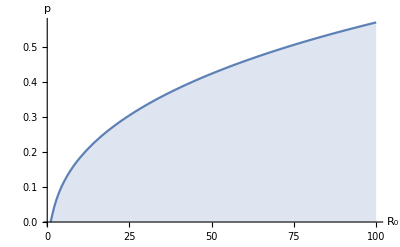

```mathematica
Plot[g[R],{R,0,100},Filling->Bottom,AxesLabel->{Subscript[R, 0],p},PlotRange->All]
```

LogLinearPlot::invpr: Value of option PlotRange should be positive in the scaled dimensions.

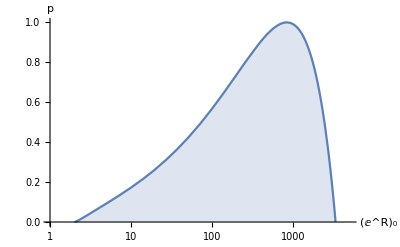

```mathematica
LogLinearPlot[h[R],{R,0.001,10000},Filling->Bottom,AxesLabel->{Subscript[R, 0],p},PlotRange->{{0,5000},{0,1}}]
```

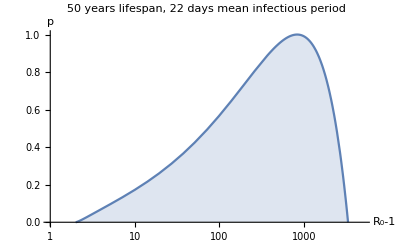

```mathematica
Show[%57,AxesLabel->{HoldForm[Subscript[R, 0]-1],p},PlotLabel->RawBoxes[RowBox[{RowBox[{"50"," ","years"," ","lifespan"}],","," ",RowBox[{"22"," ","days"," ","mean"," ","infectious"," ","period"}]}]],LabelStyle->{GrayLevel[0]}]
```